```mathematica
Manipulate[Plot[(1/2)/(1-Exp[s*t/2]*(1-1/(2x)))/. {s->0.005},{t,-2000,2000},
PlotRange ->{{-2000,2000},{0,1}}],{x,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
Clear[t]
```

```mathematica
t[x]= (Sqrt[Ne * π / (2s)]*Exp[2 Ne s(x-1/2)^2](Erf[Sqrt[Ne s / 2]]+Erf[Sqrt[Ne s / 2](1-2x)])((Erf[Sqrt[Ne s / 2]]-Erf[Sqrt[Ne s / 2](1-1/Ne)])))/(Erf[Sqrt[Ne s / 2]]x(1-x))
```

(ⅇ^(2 Ne s (-1/2+x)^2) √(π/2) √(Ne/s) (Erf[(√(Ne s))/(√2)]-Erf[((1-1/Ne) √(Ne s))/(√2)]) (Erf[(√(Ne s))/(√2)]+Erf[(√(Ne s) (1-2 x))/(√2)]))/((1-x) x Erf[(√(Ne s))/(√2)])

```mathematica
Manipulate[Plot[Evaluate[(Sqrt[Ne * π / (2s)]*Exp[2 Ne s(x-1/2)^2](Erf[Sqrt[Ne s / 2]]+Erf[Sqrt[Ne s / 2](1-2x)])((Erf[Sqrt[Ne s / 2]]-Erf[Sqrt[Ne s / 2](1-1/Ne)])))/(Erf[Sqrt[Ne s / 2]]x(1-x))/.{Ne->10^4}], {x,0,1},PlotRange->{{0,1},{0,20}}],{s,0,0.005}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
(*weird things happen for large effect sizes. I think this is due to numerical precision with the difference in error functions*)
```

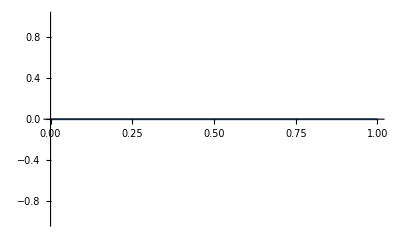

```mathematica
Plot[Evaluate[t[x]/.{Ne->10^4,s->0.007}], {x,0,1}]
```

```mathematica
(*comment one of these out and evaluate below, the first smaller number works fine, the second is evaluated at 0*)
```

```mathematica
s0=0.00612526155
```

0.00612526

```mathematica
(*s0=0.0061252616*)
```

0.00612526

```mathematica
Evaluate[t[x]/.{Ne->10^4,s->s0, x->0.0001}]
```

70226.

```mathematica
Exp[2 Ne s(x-1/2)^2]/.{Ne->10^4,s->s0, x->0.0001}
```

1.97477×10^13

```mathematica
(Erf[Sqrt[Ne s / 2]]+Erf[Sqrt[Ne s / 2](1-2x)])/.{Ne->10^4,s->s0, x->0.0001}
```

2.

```mathematica
(*i think the problem is this expression. both values of s0 show the Erfs are 1, but the difference is slightly positive for the smaller number, but 0 for the larger number, i think its just rounding*)
```

```mathematica
((Erf[Sqrt[Ne s / 2]]-Erf[Sqrt[Ne s / 2](1-1/Ne)]))/.{Ne->10^4,s->s0, x->0.0001}
```

1.11022×10^-16

```mathematica
Erf[Sqrt[Ne s / 2]]/.{Ne->10^4,s->s0, x->0.0001}
```

1.

```mathematica
Erf[Sqrt[Ne s / 2](1-1/Ne)]/.{Ne->10^4,s->s0, x->0.0001}
```

1.

```mathematica
Sqrt[Ne * π / (2s)]/.{Ne->10^4,s->s0, x->0.0001}
```

1601.39

```mathematica
(*Erf gets close to 1 fast, so large values of s have a very small difference*)
```

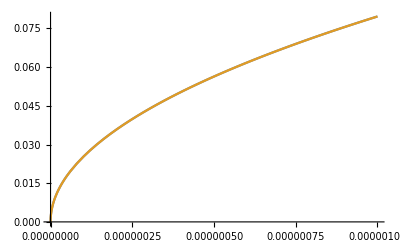

```mathematica
Plot[{Erf[Sqrt[Ne s / 2]]/.{Ne-> 10^4},
Erf[Sqrt[Ne s / 2](1-1/Ne)]/.{Ne-> 10^4}}, {s,0,0.000001}]
```

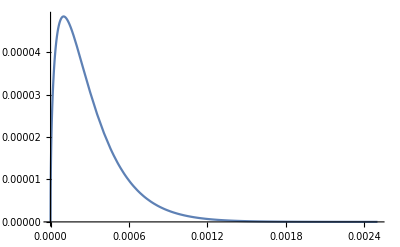

```mathematica
Plot[((Erf[Sqrt[Ne s / 2]]-Erf[Sqrt[Ne s / 2](1-1/Ne)]))/.{Ne-> 10^4}, {s,0,0.0025}]
```

```mathematica
(*supposedly the sojourn time approaches this distribution for large effect sizes, now using the popscaled selection coeff*)
Manipulate[Plot[2Exp[-s x]/x, {x,0,1}], {s,0,10}]
```